```mathematica
1.naloga
```

```mathematica
izraz=(x^5-2 x^2+3x+4)/(x^5-2x-1)
```

(4+3 x-2 x^2+x^5)/(-1-2 x+x^5)

```mathematica
izraz /.{{x ->1},{ x->2},{x->3},{x->4}}
```

{-3,34/27,119/118,144/145}

```mathematica
f[x_] :=(x^5-2 x^2+3x+4)/(x^5-2x-1)
f[1]
f[2]
f[3]
f[4]
```

-3

34/27

119/118

144/145

```mathematica
Table[f[x], {x,1, 10}]
```

```mathematica
{-3,34/27,119/118,144/145,1547/1557,7726/7763,8367/8396,32668/32751,29459/29515,99834/99979}
```

```mathematica
2.naloga
```

```mathematica
sez{10,20,30,40,50,60,70}
sez=Table[x*10, {x,7}]
```

{10,20,30,40,50,60,70}

```mathematica
Take[sez, 3]
```

{10,20,30}

```mathematica
Take[sez, 1-3]
```

{60,70}

```mathematica
Part[sez,  {2,3,4}]
```

{20,30,40}

```mathematica
Part[sez, {2,3,5}]
```

{20,30,50}

```mathematica
Drop[sez, {4,5}]
```

{10,20,30,60,70}

```mathematica
3.naloga
```

```mathematica
ClearAll[x,a]
```

```mathematica
sez{x^6,x^2,a}
sez/.x->3
sez/.x->x^2
sez/.x^2->x
sez/.x->{1,2,3}
sez/.{x->3,a->x}
sez//.{x->3,a->x}
```

Thread::tdlen: Objects of unequal length in {10,20,30,40,50,60,70} {x^6,x^2,a} cannot be combined.

{x^6,x^2,a} {10,20,30,40,50,60,70}

{10,20,30,40,50,60,70}

{10,20,30,40,50,60,70}

{10,20,30,40,50,60,70}

«3 more identical outputs»

```mathematica
4.naloga
```

```mathematica
D[x^5+4x^3-9,x]/.x->{1,5}
```

{17,3425}

```mathematica
FullSimplify[D[Abs[x+1],x], x∈Reals]
```

Sign[1+x]

```mathematica
D[ⅇ^(x^(1/4))]/.x->{1,2}
```

{ⅇ,ⅇ^(2^(1/4))}

```mathematica
D[x+1]/.x->{1,-1}
```

{2,0}

```mathematica
D[ax^2+3b]/.x->{1,2}
```

ax^2+3 b

```mathematica
5.naloga
```

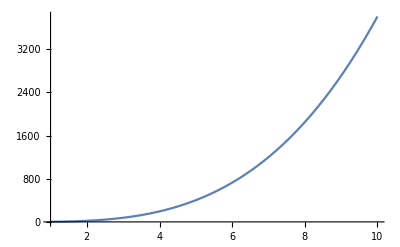

```mathematica
f[x_] :=x^3 Log[4x+5]
Plot[f[x], {x,1,10}]
```

```mathematica
x0=5
```

5

```mathematica
f[x0]
```

125 Log[25]

```mathematica
k0=D[f[x],x]/.x->x0
```

20+75 Log[25]

```mathematica
n0=n/.First[Solve[f[x0]= k0*x0+n, n]]
```